Define original Hamiltonian in the rotating frame (for resonant drive)

```mathematica
Horig:=H1/4*(sx+Cos[2*ww*t]sx-Sin[2*ww*t]*sy)
```

Define Magnus approximation Hamiltonians

```mathematica
Hww0:=(H1 sx)/4;
HwwM1:=(H1 (H1 sz+8 sx ww)+(4 H1D sy-2 H1^2 sz) Cos[2 α0]+4 H1D sx Sin[2 α0])/(32 ww);
HwwM2:=1/(256 ww^2)(8 H1 (-(H1^2 sx)/4+H1 sz ww+8 sx ww^2)+2 (H1^3 sx+8 H1DD sx+16 H1D sy ww-8 H1^2 sz ww) Cos[2 α0]-H1^3 sx Cos[4 α0]+2 (H1^3 sy-8 H1DD sy+12 H1 H1D sz+16 H1D sx ww) Sin[2 α0]+H1^3 sy Sin[4 α0]);
```

```mathematica
pms = {sx->PauliMatrix[1],sy->PauliMatrix[2],sz->PauliMatrix[3]};
vals = {ww->1};
H1Dsubs={
H1->H1[t],
H1D->D[H1[t],{t,1}],
H1DD->D[H1[t],{t,2}],
H1DDD->D[H1[t],{t,3}],
H1DDDD->D[H1[t],{t,4}]
};
AssembleH[H_,H1f_]:=(H/.vals/.H1Dsubs/.pms/.{H1->H1f});
ToHFunc[H_]:=Function[{t,α0},func]/.func->H;
GetHFunc[H_,H1f_]:=ToHFunc@AssembleH[H,H1f];
```

```mathematica
(* Numerically compute trajectory from any Hamiltonian *)
NTrajectory[Hfunc_,tM_,α0_,ψ0_]:=
Module[{},
First@NDSolve[{I*D[ψ[t],t]==Hfunc[t,α0].ψ[t],ψ[0]==ψ0},ψ,{t,0,tM}]
]

(* Helper functions for plotting *)
(* Coordinate transforms *)
BlochCoordinatesFromState=Function[{state},
{
Re[state[[1]]*state[[2]]*+state[[1]]*state[[2]]],
-Im[state[[1]]*state[[2]]*]+Im[state[[1]]**state[[2]]],
state[[1]]state[[1]]*-state[[2]]state[[2]]*
}];

RotationAxisFromHamiltonian=Function[{H},
Table[Re[Tr[H.PauliMatrix[i]]/2.],{i,1,3}]
];

(* Precompute the static bloch sphere elements (circumferences and axes) *)
BlochSphereCircles=With[{r=1},
{ParametricPlot3D[0.99*{r Cos[θ],r Sin[θ],0},{θ,0,2 π},PlotStyle->{Thin,Gray},Boxed->False,Axes->False,PerformanceGoal->"Speed"],
ParametricPlot3D[0.99*{0,r Cos[θ],r Sin[θ]},{θ,0,2 π},PlotStyle->{Thin,Gray},Boxed->False,Axes->False,PerformanceGoal->"Speed"],
ParametricPlot3D[0.99*{r Cos[θ],0,r Sin[θ]},{θ,0,2 π},PlotStyle->{Thin,Gray},Boxed->False,Axes->False,PerformanceGoal->"Speed"]}
];
BlochSphereAxes=With[{r=1},{
Graphics3D[{
Thin, Gray, Dashed,
Line[{{-1.,0.,0.},{1.,0.,0.}}],
Line[{{0.,-1.,0.},{0.,1.,0.}}],
Line[{{0.,0.,-1.},{0.,0.,1.}}]
}]
}];

(* Plot trace on Bloch sphere *)
ClearAll[PlotBlochTraceFromState]
Options[PlotBlochTraceFromState]={PlotRange->{{-1,1},{-1,1},{-1,1}}};
PlotBlochTraceFromState[ψ_,range_,opts :OptionsPattern[{PlotBlochTraceFromState,ParametricPlot3D}]]:=
Module[{},
ParametricPlot3D[
BlochCoordinatesFromState[ψ[t]],
Evaluate[Join[{t},range]],
opts, Evaluate[Sequence@@Options[PlotBlochTraceFromState]]
]
];

(* Plot a vector from the center of the Bloch sphere to the surface for a given state ψ *)
PlotBlochVectorFromState[ψ_,style_List :{}]:=PlotBlochVector[BlochCoordinatesFromState[ψ],style];

(* Plot a vector from the center of the Bloch sphere to the {x, y, z} coordinates given by vec *)
PlotBlochVector[vec_,style_List : {}]:=
Graphics3D[Evaluate[Join[
style,
{Line[{{0.,0.,0.},vec}]}
]]];

(* Plot points given by a list of {x, y, z} tuples in pts *)
PlotBlochPoints[pts_,style_List : {}]:=
Graphics3D[Evaluate[Join[
style,
{Point[pts]}
]]];

(* Plot points given by a list of state vectors ψs *)
PlotBlochPointsFromStates[ψs_,style_List : {}]:=PlotBlochPoints[Map[BlochCoordinatesFromState,ψs],style]
```

## 3D plots

Time for some plotting!

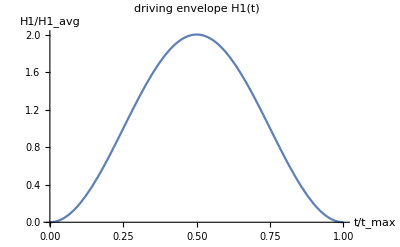
| -Graphics-

```mathematica
H1profile=Function[t,(1-Cos[2*Pi*t/tMaxIn])*H1avgIn];

H1preview=H1profile/.{tMaxIn->1.,H1avgIn->1.};

Grid[{{
DynamicModule[{origTrace, o0Trace, o1Trace, o2Trace,ψ0,gateAngle,tMax,H1func,hOrigFunc,oMax,oTraces,oColors,tCoincidence,t0,tC,relevantTCoincidence},
Manipulate[
(* Define initial state and desired gate angle *)
ψ0={1,0};
(*H1avg=0.2;*)
gateAngle = Pi;
tMax = 2*gateAngle/H1avg;
H1func=H1profile/.{tMaxIn->tMax,H1avgIn->H1avg};

(* Compute the times at which the Magnus and the real Hamiltonians are supposed to coincide *)
t0=(α0/ww)/.vals; (* ww is still defined in vals, maybe later we make it an interactive parameter as well? *)
tC=(Pi/ww)/.vals;
tCoincidence=t0+Range[0.0,tMax,tC];

(* Assemble Hamiltonians based on the given parameters and numerically solve trajectories of qubit *)
hOrigFunc=GetHFunc[Horig,H1func];
origTrace=ψ/.NTrajectory[hOrigFunc,tMax,α0,ψ0];
o0Trace=ψ/.NTrajectory[GetHFunc[Hww0,H1func],tMax,α0,ψ0];
o1Trace=ψ/.NTrajectory[GetHFunc[HwwM1,H1func],tMax,α0,ψ0];
o2Trace=ψ/.NTrajectory[GetHFunc[HwwM2,H1func],tMax,α0,ψ0];
oTraces={o0Trace,o1Trace,o2Trace};
oMax=Length[oTraces];
oColors=Array[ColorData["DeepSeaColors"],oMax,{0.,1.}];

(* Let's get plottin'! *)

Dynamic[
relevantTCoincidence=Select[tCoincidence,(#<tM*tMax&)];
Show[
Join[
{ (* Plot the trajectory, state vector and instantaneous rotation axis of the qubit under the original Hamiltonian *)
PlotBlochTraceFromState[origTrace,{0,tM*tMax},{PlotStyle->Red}],
PlotBlochVectorFromState[origTrace[tM*tMax],{Red, Thickness[0.015]}],
PlotBlochVector[RotationAxisFromHamiltonian[hOrigFunc[tM*tMax,0.0]],{Red,Thickness[0.015],Dashed}]
},
(* Plot the trajectory of the qubit under the approximate Hamiltonians *)
Table[PlotBlochTraceFromState[oTraces[[i]],{0,tM*tMax},{PlotStyle->oColors[[i]]}],{i,upToOrder+1}],
(* Plot the points where the approximate trajectories (should) coincide with the original trajectory *)
Table[PlotBlochPointsFromStates[Map[oTraces[[i]],relevantTCoincidence],{PointSize[Large],oColors[[i]]}],{i,upToOrder+1}],
(* Add static Bloch sphere elements *)
BlochSphereCircles,
BlochSphereAxes
],
ImageSize->{500,500},
ViewAngle->Pi/10,
Axes->False,
Boxed->False
]
]
,
{{tM, 0.01,"Time t"},0.01,1.0,Appearance->"Open",AnimationRate->.03,RefreshRate->.005},
{{α0,0.0,"Offset α0"},0.0, Pi,Appearance->"Open"},
{{H1avg, 0.2,"Average drive strength H1_avg"},0.01,1.0,Appearance->"Open"},
{{upToOrder,1,"Include Magnus expansion up to order"},-1,2,1,Appearance->"Open"}
]
],
Plot[H1preview[t],{t,0,1},ImageSize->{400,400},AxesLabel->{"t/t_max","H1/H1_avg"},PlotLabel->"driving envelope H1(t)"]
}},
Alignment->Bottom
]
```

```mathematica
(* Mercator projection plotting *)

PolarCoordinatesFromState=Function[{state},
{
2*ArcCos[Abs[state[[1]]]],
Arg[state[[2]]]-Arg[state[[1]]]
}
];

MercatorCoordinatesFromPolar=Function[{coords},
{
coords[[1]],
ArcTanh[Sin[coords[[2]]+Pi/2]]
}
];
```

## Polar plots

```mathematica
Grid[{{
DynamicModule[{origTrace, o0Trace, o1Trace, o2Trace,ψ0,gateAngle,tMax,H1func,hOrigFunc,oMax,oTraces,oColors,tCoincidence,t0,tC,relevantTCoincidence},
Manipulate[
(* Define initial state and desired gate angle *)
ψ0={1,0};
(*H1avg=0.2;*)
gateAngle = Pi;
tMax = 2*gateAngle/H1avg;
H1func=H1profile/.{tMaxIn->tMax,H1avgIn->H1avg};

(* Compute the times at which the Magnus and the real Hamiltonians are supposed to coincide *)
t0=(α0/ww)/.vals; (* ww is still defined in vals, maybe later we make it an interactive parameter as well? *)
tC=(Pi/ww)/.vals;
tCoincidence=t0+Range[0.0,tMax,tC];

(* Assemble Hamiltonians based on the given parameters and numerically solve trajectories of qubit *)
hOrigFunc=GetHFunc[Horig,H1func];
origTrace=ψ/.NTrajectory[hOrigFunc,tMax,α0,ψ0];
o0Trace=ψ/.NTrajectory[GetHFunc[Hww0,H1func],tMax,α0,ψ0];
o1Trace=ψ/.NTrajectory[GetHFunc[HwwM1,H1func],tMax,α0,ψ0];
o2Trace=ψ/.NTrajectory[GetHFunc[HwwM2,H1func],tMax,α0,ψ0];
oTraces={o0Trace,o1Trace,o2Trace};
oMax=Length[oTraces];
oColors=Array[ColorData["DeepSeaColors"],oMax,{0.,1.}];

(* Let's get plottin'! *)

Dynamic[
relevantTCoincidence=Select[tCoincidence,(#<tM*tMax&)];
Show[
Join[
{ (* Plot the trajectory, state vector and instantaneous rotation axis of the qubit under the original Hamiltonian *)
ParametricPlot[PolarCoordinatesFromState[origTrace[t]],{t,0,tM*tMax},PlotStyle->Red]
(*PlotBlochTraceFromState[origTrace,{0,tM*tMax},{PlotStyle->Red}],
PlotBlochVectorFromState[origTrace[tM*tMax],{Red, Thickness[0.015]}],
PlotBlochVector[RotationAxisFromHamiltonian[hOrigFunc[tM*tMax,0.0]],{Red,Thickness[0.015],Dashed}]*)
},
(* Plot the trajectory of the qubit under the approximate Hamiltonians *)
Table[ParametricPlot[PolarCoordinatesFromState[oTraces[[i]][t]],{t,0,tM*tMax},PlotStyle->oColors[[i]]],{i,upToOrder+1}],
(* Plot the points where the approximate trajectories (should) coincide with the original trajectory *)
Table[Graphics[{PointSize[Large],oColors[[i]],Point[PolarCoordinatesFromState/@(oTraces[[i]]/@relevantTCoincidence)]}],{i,upToOrder+1}],
{Graphics[{PointSize[Large],Red,Opacity[0.5],Point[PolarCoordinatesFromState/@(origTrace/@relevantTCoincidence)]}]}
],
PlotRange->{{0,Pi},{-Pi,Pi}},
AxesOrigin->{0,-Pi},
AspectRatio->1,
ImageSize->{500,500},
AxesLabel->{"population angle θ","phase angle ϕ"}
]
]
,
{{tM, 0.01,"Time t"},0.01,1.0,Appearance->"Open",AnimationRate->.03,RefreshRate->.005},
{{α0,0.0,"Offset α0"},0.0, Pi,Appearance->"Open"},
{{H1avg, 0.2,"Average drive strength H1_avg"},0.01,1.0,Appearance->"Open"},
{{upToOrder,1,"Include Magnus expansion up to order"},-1,2,1,Appearance->"Open"}
]
],
Plot[H1preview[t],{t,0,1},ImageSize->{400,400},AxesLabel->{"t/t_max","H1/H1_avg"},PlotLabel->"driving envelope H1(t)"]
}},
Alignment->Bottom
]
```

| -Graphics-

## Mercator plots

```mathematica
Grid[{{
DynamicModule[{origTrace, o0Trace, o1Trace, o2Trace,ψ0,gateAngle,tMax,H1func,hOrigFunc,oMax,oTraces,oColors,tCoincidence,t0,tC,relevantTCoincidence},
Manipulate[
(* Define initial state and desired gate angle *)
ψ0={1,0};
(*H1avg=0.2;*)
gateAngle = Pi;
tMax = 2*gateAngle/H1avg;
H1func=H1profile/.{tMaxIn->tMax,H1avgIn->H1avg};

(* Compute the times at which the Magnus and the real Hamiltonians are supposed to coincide *)
t0=(α0/ww)/.vals; (* ww is still defined in vals, maybe later we make it an interactive parameter as well? *)
tC=(Pi/ww)/.vals;
tCoincidence=t0+Range[0.0,tMax,tC];

(* Assemble Hamiltonians based on the given parameters and numerically solve trajectories of qubit *)
hOrigFunc=GetHFunc[Horig,H1func];
origTrace=ψ/.NTrajectory[hOrigFunc,tMax,α0,ψ0];
o0Trace=ψ/.NTrajectory[GetHFunc[Hww0,H1func],tMax,α0,ψ0];
o1Trace=ψ/.NTrajectory[GetHFunc[HwwM1,H1func],tMax,α0,ψ0];
o2Trace=ψ/.NTrajectory[GetHFunc[HwwM2,H1func],tMax,α0,ψ0];
oTraces={o0Trace,o1Trace,o2Trace};
oMax=Length[oTraces];
oColors=Array[ColorData["DeepSeaColors"],oMax,{0.,1.}];

(* Let's get plottin'! *)

Dynamic[
relevantTCoincidence=Select[tCoincidence,(#<tM*tMax&)];
Show[
Join[
{ (* Plot the trajectory, state vector and instantaneous rotation axis of the qubit under the original Hamiltonian *)
ParametricPlot[MercatorCoordinatesFromPolar[PolarCoordinatesFromState[origTrace[t]]],{t,0,tM*tMax},PlotStyle->Red]
(*PlotBlochTraceFromState[origTrace,{0,tM*tMax},{PlotStyle->Red}],
PlotBlochVectorFromState[origTrace[tM*tMax],{Red, Thickness[0.015]}],
PlotBlochVector[RotationAxisFromHamiltonian[hOrigFunc[tM*tMax,0.0]],{Red,Thickness[0.015],Dashed}]*)
},
(* Plot the trajectory of the qubit under the approximate Hamiltonians *)
Table[ParametricPlot[MercatorCoordinatesFromPolar[PolarCoordinatesFromState[oTraces[[i]][t]]],{t,0,tM*tMax},PlotStyle->oColors[[i]]],{i,upToOrder+1}]
(* Plot the points where the approximate trajectories (should) coincide with the original trajectory *)
(*Table[Graphics[{PointSize[Large],oColors[[i]],Point[MercatorCoordinatesFromPolar/@PolarCoordinatesFromState/@(oTraces[[i]]/@relevantTCoincidence)]}],{i,upToOrder+1}]*)
],
AspectRatio->1,
ImageSize->{500,500},
AxesLabel->{"phase angle ϕ","population angle θ"}
]
]
,
{{tM, 0.01,"Time t"},0.01,1.0,Appearance->"Open",AnimationRate->.03,RefreshRate->.005},
{{α0,0.0,"Offset α0"},0.0, Pi,Appearance->"Open"},
{{H1avg, 0.2,"Average drive strength H1_avg"},0.01,1.0,Appearance->"Open"},
{{upToOrder,1,"Include Magnus expansion up to order"},-1,2,1,Appearance->"Open"}
]
],
Plot[H1preview[t],{t,0,1},ImageSize->{400,400},AxesLabel->{"t/t_max","H1/H1_avg"},PlotLabel->"driving envelope H1(t)"]
}},
Alignment->Bottom
]
```

| -Graphics-